## Coupled ODE

### Harmonic Oscillator

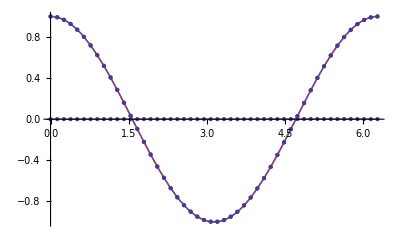

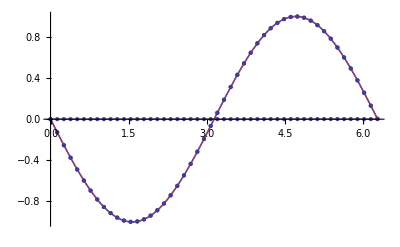

```mathematica
period= 6.28;
steps = 16;
ti = NDSolve[{s'[t] == v[t], v'[t] == -1* s[t]  , s[0] == 1.0,v[0] == 0.0}, {s,v}, {t,0,period}, StartingStepSize -> (period/steps),Method ->{"FixedStep",Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 4}}];

Plot[{Evaluate[s[t]/.ti],Cos[t], Abs[ Evaluate[s[t]/.ti]-Cos[t]]},{t,0,period},PlotRange->All, Mesh->Full]
Plot[{Evaluate[v[t]/.ti],-Sin[t],Abs[ Evaluate[s[t]/.ti]-Cos[t]]},{t,0,period},PlotRange->All, Mesh->Full]
```

```mathematica
fi= NDSolve[{s'[t]==v[t],v'[t]==-s[t],s[0]==1.,v[0]==0.},{s,v},{t,0,10},StartingStepSize->0.1,Method->{"FixedStep",Method->{"ExplicitEuler"}}];
```

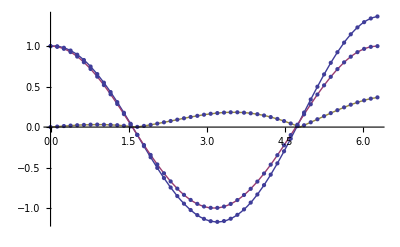

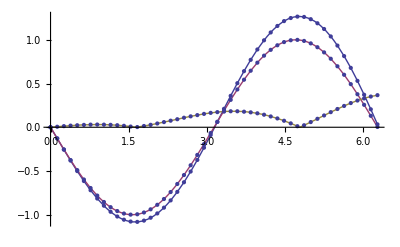

```mathematica
Plot[{Evaluate[s[t] /.fi],Cos[t],Abs[ Evaluate[s[t] /.fi]-Cos[t]]},{t,0,period},PlotRange->All, Mesh->Full]
Plot[{Evaluate[v[t] /.fi],-Sin[t],Abs[ Evaluate[s[t] /.fi]-Cos[t]]},{t,0,period},PlotRange->All, Mesh->Full]
```

### Lottka- Voltera

We've implemented the Lottka-Voltera prey-predator model. A simulation is shown below. We have used Solve to find the stable point for these populations, which is with y = 50 and x = 10. We've plotted the population change twice, first with initial populations close to the stable point, and the second time with positions further off.

{{y→0.,x→0.},{y→50.,x→10.}}

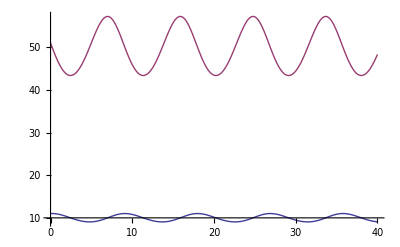

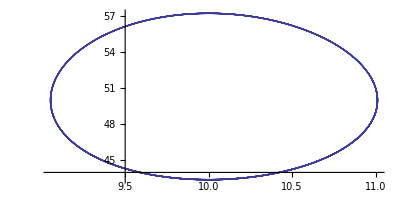

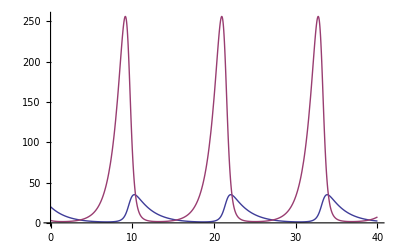

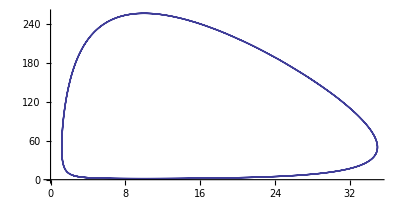

```mathematica
Solve[{-0.5 * x + 0.1 * 0.1 * x * y == 0, 1 * y - 0.1 * x * y == 0}]


pp = NDSolve[{x'[t] == -0.5 * x[t] + 0.1 * 0.1 * x[t] * y[t], y'[t] == 1 * y[t] - 0.1 * x[t] * y[t], x[0] == 11, y[0] == 51}, {x,y}, {t, 40} ];
Plot[{Evaluate[x[t]/.pp],Evaluate[y[t]/.pp] },{t,0, 40},PlotRange->All]
ParametricPlot[Evaluate[{x[t], y[t]} /. pp], {t, 0, 40}, AspectRatio -> 1/2]

pp = NDSolve[{x'[t] == -0.5 * x[t] + 0.1 * 0.1 * x[t] * y[t], y'[t] == 1 * y[t] - 0.1 * x[t] * y[t], x[0] == 20, y[0] == 3}, {x,y}, {t, 40} ];
Plot[{Evaluate[x[t]/.pp],Evaluate[y[t]/.pp] },{t,0, 40},PlotRange->All]
ParametricPlot[Evaluate[{x[t], y[t]} /. pp], {t, 0, 40}, AspectRatio -> 1/2]
```

### Modified Prey-Predator model

We've now modified the Lottka - Voltera model used in the previous section according to Verhulst's model. (For when there are no predators). As you can see in the graph below, the predators die out, and the prey population always stabilizes at 10, which is the stable point for this set of equations.

{{x→-4.8,y→50.},{x→0.,y→-10.},{x→0.,y→10.}}

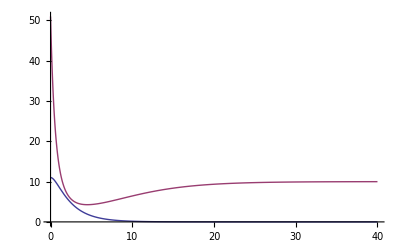

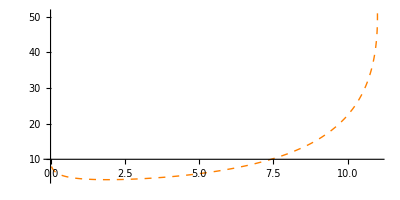

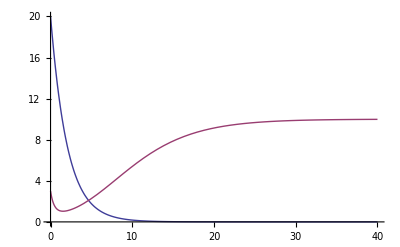

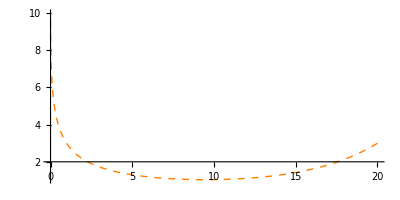

```mathematica
Solve[{-0.5 * x + 0.1 * 0.1 * x * y == 0, 1 * (1 - (y / 100) * y)- 0.1 * x * y == 0}]


pp = NDSolve[{x'[t] == -0.5 * x[t] + 0.1 * 0.1 * x[t] * y[t], y'[t] == 1 * (1 - (y[t] / 100) * y[t]) - 0.1 * x[t] * y[t], x[0] == 11, y[0] == 51}, {x,y}, {t, 40} ];
Plot[{Evaluate[x[t]/.pp],Evaluate[y[t]/.pp] },{t,0, 40},PlotRange->All]
ParametricPlot[Evaluate[{x[t], y[t]} /. pp], {t, 0, 40}, AspectRatio -> 1/2, PlotRange -> All, PlotStyle -> {Orange, Dashed, Thick}]

pp = NDSolve[{x'[t] == -0.5 * x[t] + 0.1 * 0.1 * x[t] * y[t], y'[t] == 1 * (1 - (y[t] / 100) * y[t]) - 0.1 * x[t] * y[t], x[0] == 20, y[0] == 3}, {x,y}, {t, 40} ];
Plot[{Evaluate[x[t]/.pp],Evaluate[y[t]/.pp] },{t,0, 40},PlotRange->All]
ParametricPlot[Evaluate[{x[t], y[t]} /. pp], {t, 0, 40}, AspectRatio -> 1/2, PlotRange -> All, PlotStyle -> {Orange, Dashed, Thick}]
```

### Gilpin's Model

This is a model for a system with 2 prey species, and one predator. The preys compete with each other for food, in addition to the Lottka-Volterra predator-prey relation.
We've plotted the result of these functions. As you can see in the first graph, the population of prey X is mostly dominant (red), but sometimes the predator Z (yellow) acts up and consumes a lot of preys. This benefits prey Y (blue) who then grows. 
From this, we can conclude that prey Y is mostly influenced by the population of X, while X is mostly influenced by predator Z. This also shows in the given equations for X and Y.
We have also plotted the scatterplots of X vs Y, Y vs Z and X vs Z. We see that these populations exhibit chaotic behaviour. There seems to be some kind of a pattern for the relations, but it changes some each cycle. It's similar but not the same.  □

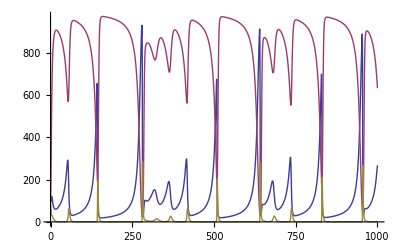

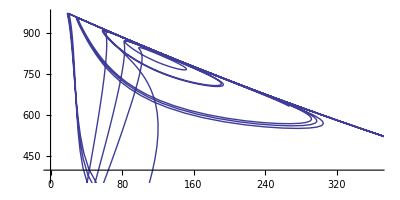

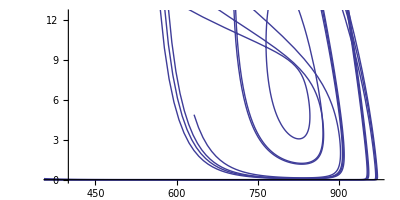

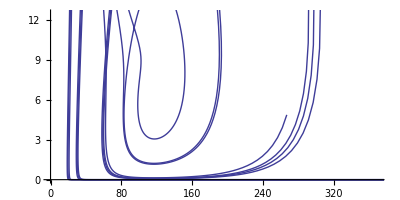

```mathematica
pp = NDSolve[{x'[t] == x[t] * (1 - 0.001 * x[t] - 0.001 * y[t] - 0.01 * z[t]), y'[t] == y[t] * (1 - 0.001 * y[t] - 0.0015 * x[t] - 0.001 * z[t]), z'[t] == z[t] * (0.005 * x[t] + 0.0005 * y[t] - 1), x[0] == 100, y[0] == 100, z[0] == 100}, {x,y,z}, {t, 1000}];
Plot[{Evaluate[x[t]/.pp],Evaluate[y[t]/.pp], Evaluate[z[t]/.pp]  },{t,0,1000},PlotRange->All]
ParametricPlot[Evaluate[{x[t], y[t]} /. pp], {t, 0, 1000}, AspectRatio -> 1/2]
ParametricPlot[Evaluate[{y[t], z[t]} /. pp], {t, 0, 1000}, AspectRatio -> 1/2]
ParametricPlot[Evaluate[{x[t], z[t]} /. pp], {t, 0, 1000}, AspectRatio -> 1/2]
```

### Malaria

{474.516}

{26.439}

{1.04525}

{981.12}

{19.8803}

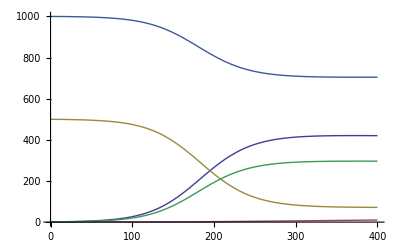

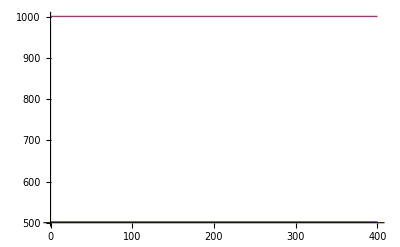

```mathematica
a = 0.0001;
b = 0.005;
c = 0.0001;
d = 10*a;
e = a;

sys = NDSolve[{
Hi'[t] ==(a * Hu[t] * Mi[t]) - b * Hi[t] - c*Hi[t],
Hr'[t] ==  c*Hi[t] - d (Hr[t]/Mi[t]),
Hu'[t] ==  d (Hr[t]/Mi[t]) - (a * Hu[t] * Mi[t]) + b * Hi[t],

Mi'[t] == e * Mu[t]*Hi[t] - 0.1*Mi[t],
Mu'[t] == 0.1*Mi[t] -  e * Mu[t]*Hi[t],  
Hi[0] == 1, Hr[0] == 1, Hu[0] == 500, Mi[0] == 1, Mu[0] == 1000}, {Hi, Hr, Hu, Mi, Mu}, {t, 400}];

x := 100;
Evaluate[Hu[x]/.sys]
Evaluate[Hi[x]/.sys]
Evaluate[Hr[x]/.sys]
Evaluate[Mu[x]/.sys]
Evaluate[Mi[x]/.sys]


Plot[{Evaluate[Hi[t]/.sys],Evaluate[Hr[t]/.sys], Evaluate[Hu[t]/.sys] , Evaluate[Mi[t]/.sys], Evaluate[Mu[t]/.sys] },{t,0,400},PlotRange->All]

Plot[{Evaluate[Hi[t]/.sys]+Evaluate[Hr[t]/.sys]+ Evaluate[Hu[t]/.sys] , Evaluate[Mi[t]/.sys]+ Evaluate[Mu[t]/.sys] },{t,0,400},PlotRange->All]
```